```mathematica
D2a[n_,k_]:=D2a[n,k]=Sum[D2a[Floor[n/j],k-1],{j,2,n}];D2a[n_,0]:=1
E2a[n_,k_, a_]:= E2a[n,k,a]=Sum[ E2a[n/j,k-1,a],{j,2,n}]-Sum[ E2a[n/(a j),k-1,a],{j,1,n/a}];E2a[n_,0,a_]:=1
Lina[n_,a_]:=Sum[ (-1)^(k+1)/k E2a[n,k,a],{k,1,Log[If[a<2,a,2],n]}]
Lin[n_]:=Sum[ (-1)^(k+1)/k D2a[n,k],{k,1,Log[2,n]}]
```

```mathematica
Lin[100]-Lina[100,11/10]
```

282000222059796592919/63245806209101973600

```mathematica
Lina[100,2]
```

313/12

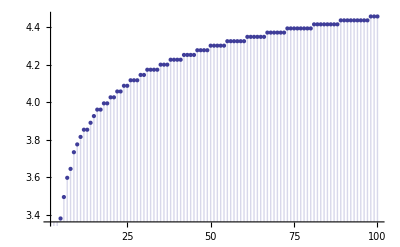

```mathematica
DiscretePlot[ Lin[n]-Lina[n,11/10],{n,2,100}]
```

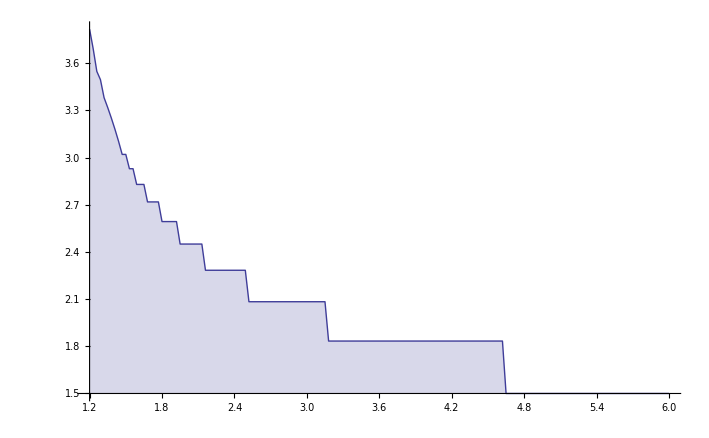

```mathematica
DiscretePlot[ Lin[100]-Lina[100,n],{n,1.2,6,.03}]
```